```mathematica
Remove["Global`*"];
ClearAll[simulatePopulations]
```

```mathematica
simulatePopulations[initialDoves_, initialHawks_, numLists_, numIterations_, printing_: 0] := Module[
    {doves = initialDoves, hawks = initialHawks, lists, processInteractions, 
     addToList, initializeLists, printTable = {{"Iteration", "Doves", "Hawks", 
        "Ratio of Doves", "One Dove", "One Hawk", "Two Doves", "Two Hawks", "D&H"}}, 
     oneDove, oneHawk, twoDoves, twoHawks, doveAndHawk},
    
    initializeLists[count_] := Table[{}, {count}];
    
    addToList[listOfLists_, element_] := Module[
        {availableLists, randomIndex, updatedList = listOfLists},
        availableLists = Select[Range[Length[updatedList]], Length[updatedList[[#]]] < 2 &];
        If[Length[availableLists] > 0,
            randomIndex = RandomChoice[availableLists];
            updatedList[[randomIndex]] = Append[updatedList[[randomIndex]], element];
            updatedList,
            Print["All lists are full."];
            listOfLists
        ]
    ];
    
    processInteractions[pairs_] := Module[{newDoves = 0, newHawks = 0, u=RandomReal[]},
        Do[
            Switch[pair,
                {1}, newDoves += 2; oneDove++,
                {2}, newHawks += 2; oneHawk++,
                {1, 1}, newDoves += 2; twoDoves++,
              
      {2, 2},Null; twoHawks++,
                {1, 2} | {2, 1},
                If[RandomReal[] < 0.5, newHawks += 1, newHawks += 2];
                If[RandomReal[] < 0.5, newDoves += 0, newDoves += 1];
                doveAndHawk++
            ],
            {pair, pairs}
        ];
        {newDoves, newHawks}
    ];
    
    appendToTable[iter_, doves_, hawks_] := Module[{total = doves + hawks, ratio},
        ratio = If[total > 0, N[doves/total], 0];
        AppendTo[printTable, {iter, doves, hawks, ratio, oneDove, oneHawk, twoDoves, twoHawks, doveAndHawk}]
    ];
    
    lists = initializeLists[numLists];
    
    For[i = 1, i ≤ numIterations && (doves > 0 || hawks > 0), i++,
        oneDove = 0; oneHawk = 0; twoDoves = 0; twoHawks = 0; doveAndHawk = 0;
        While[doves > 0 || hawks > 0,
            If[Length@Position[lists, l_List /; Length[l] < 2] == 0,
                (*Print[lists];*)
                (*Print["Failed to add elements: All lists are full."];*)
                Break[]
            ];
            rand = RandomChoice[{doves, hawks} -> {1, 2}];
            If[rand == 1,
                lists = addToList[lists, 1];
                doves--,
                lists = addToList[lists, 2];
                hawks--
            ]
        ];
        {doves, hawks} = processInteractions[lists];
        appendToTable[i, doves, hawks];
        lists = initializeLists[numLists]
    ];
    
    If[printing == 1,
        Print[Grid[printTable, Frame -> All, Alignment -> Center, 
          Background -> {None, {LightBlue, None}}]]
    ];
    
    {printTable}
]
```

```mathematica
simulatePopulations[10,10,100,90,1];
```

Iteration | Doves | Hawks | Ratio of Doves | One Dove | One Hawk | Two Doves | Two Hawks | D&H
1 | 18 | 20 | 0.473684 | 8 | 10 | 1 | 0 | 0
2 | 28 | 29 | 0.491228 | 12 | 12 | 1 | 2 | 4
3 | 45 | 44 | 0.505618 | 21 | 18 | 1 | 3 | 5
4 | 57 | 63 | 0.475 | 22 | 19 | 3 | 4 | 17
5 | 61 | 79 | 0.435714 | 21 | 19 | 5 | 9 | 26
6 | 60 | 85 | 0.413793 | 14 | 22 | 10 | 15 | 27
7 | 64 | 74 | 0.463768 | 18 | 15 | 6 | 20 | 30
8 | 66 | 68 | 0.492537 | 18 | 14 | 9 | 16 | 28
9 | 67 | 81 | 0.452703 | 17 | 19 | 10 | 10 | 29
10 | 68 | 61 | 0.527132 | 16 | 10 | 10 | 20 | 31
11 | 77 | 57 | 0.574627 | 20 | 15 | 15 | 14 | 18
12 | 81 | 70 | 0.536424 | 22 | 14 | 13 | 7 | 29
13 | 77 | 73 | 0.513333 | 14 | 13 | 17 | 12 | 33
14 | 67 | 80 | 0.455782 | 10 | 10 | 15 | 13 | 37
15 | 54 | 96 | 0.36 | 7 | 18 | 11 | 12 | 38
16 | 50 | 66 | 0.431034 | 10 | 12 | 8 | 28 | 28
17 | 62 | 52 | 0.54386 | 14 | 16 | 12 | 19 | 12
18 | 68 | 61 | 0.527132 | 15 | 13 | 13 | 9 | 21
19 | 74 | 66 | 0.528571 | 17 | 18 | 15 | 11 | 21
20 | 72 | 73 | 0.496552 | 15 | 9 | 11 | 10 | 37
21 | 69 | 65 | 0.514925 | 13 | 12 | 15 | 16 | 29
22 | 75 | 68 | 0.524476 | 15 | 15 | 15 | 13 | 24
23 | 75 | 54 | 0.581395 | 15 | 12 | 18 | 16 | 24
24 | 73 | 81 | 0.474026 | 19 | 18 | 13 | 3 | 30
25 | 66 | 60 | 0.52381 | 6 | 12 | 21 | 22 | 25
26 | 70 | 72 | 0.492958 | 19 | 15 | 10 | 9 | 27
27 | 78 | 61 | 0.561151 | 16 | 12 | 15 | 18 | 24
28 | 89 | 69 | 0.563291 | 23 | 16 | 15 | 10 | 25
29 | 78 | 78 | 0.5 | 11 | 11 | 19 | 9 | 40
30 | 77 | 89 | 0.463855 | 12 | 18 | 15 | 12 | 36
31 | 72 | 67 | 0.517986 | 9 | 11 | 19 | 24 | 30
32 | 66 | 90 | 0.423077 | 11 | 20 | 13 | 6 | 35
33 | 57 | 71 | 0.445313 | 10 | 8 | 10 | 23 | 36
34 | 65 | 74 | 0.467626 | 16 | 22 | 10 | 14 | 21
35 | 56 | 71 | 0.440945 | 9 | 14 | 12 | 14 | 32
36 | 56 | 84 | 0.4 | 12 | 19 | 8 | 12 | 28
37 | 58 | 77 | 0.42963 | 13 | 19 | 9 | 20 | 25
38 | 54 | 87 | 0.382979 | 12 | 23 | 9 | 13 | 28
39 | 53 | 71 | 0.427419 | 16 | 13 | 4 | 22 | 30
40 | 50 | 73 | 0.406504 | 13 | 15 | 6 | 14 | 28
41 | 58 | 69 | 0.456693 | 15 | 18 | 7 | 17 | 21
42 | 55 | 62 | 0.470085 | 10 | 11 | 11 | 16 | 26
43 | 64 | 52 | 0.551724 | 17 | 14 | 11 | 16 | 16
44 | 74 | 69 | 0.517483 | 20 | 16 | 11 | 7 | 22
45 | 70 | 66 | 0.514706 | 14 | 13 | 16 | 14 | 28
46 | 76 | 67 | 0.531469 | 21 | 9 | 8 | 12 | 33
47 | 81 | 67 | 0.547297 | 19 | 10 | 13 | 13 | 31
48 | 79 | 86 | 0.478788 | 13 | 17 | 19 | 10 | 30
49 | 75 | 69 | 0.520833 | 11 | 8 | 17 | 22 | 34
50 | 69 | 63 | 0.522727 | 14 | 10 | 16 | 15 | 29
51 | 79 | 62 | 0.560284 | 12 | 12 | 15 | 12 | 27
52 | 79 | 82 | 0.490683 | 13 | 14 | 16 | 7 | 34
53 | 72 | 69 | 0.510638 | 11 | 8 | 15 | 18 | 38
54 | 72 | 79 | 0.476821 | 17 | 16 | 12 | 11 | 31
55 | 65 | 61 | 0.515873 | 12 | 9 | 16 | 21 | 28
56 | 67 | 76 | 0.468531 | 17 | 15 | 9 | 8 | 30
57 | 65 | 69 | 0.485075 | 12 | 13 | 13 | 17 | 29
58 | 72 | 62 | 0.537313 | 20 | 14 | 10 | 15 | 25
59 | 79 | 63 | 0.556338 | 17 | 13 | 14 | 11 | 27
60 | 74 | 87 | 0.459627 | 14 | 20 | 17 | 6 | 31
61 | 70 | 58 | 0.546875 | 10 | 7 | 17 | 25 | 30
62 | 77 | 59 | 0.566176 | 19 | 13 | 13 | 10 | 25
63 | 75 | 77 | 0.493421 | 15 | 13 | 15 | 7 | 32
64 | 72 | 69 | 0.510638 | 14 | 8 | 11 | 15 | 39
65 | 65 | 70 | 0.481481 | 9 | 16 | 18 | 13 | 27
66 | 75 | 67 | 0.528169 | 20 | 15 | 11 | 16 | 23
67 | 74 | 82 | 0.474359 | 14 | 16 | 16 | 11 | 29
68 | 70 | 84 | 0.454545 | 10 | 20 | 18 | 17 | 28
69 | 67 | 57 | 0.540323 | 10 | 10 | 17 | 24 | 26
70 | 72 | 56 | 0.5625 | 17 | 13 | 14 | 11 | 22
71 | 82 | 44 | 0.650794 | 20 | 10 | 16 | 13 | 20
72 | 98 | 54 | 0.644737 | 25 | 7 | 16 | 6 | 25
73 | 97 | 59 | 0.621795 | 13 | 9 | 28 | 8 | 29
74 | 91 | 60 | 0.602649 | 10 | 10 | 29 | 10 | 29
75 | 92 | 60 | 0.605263 | 14 | 9 | 25 | 12 | 27
76 | 83 | 72 | 0.535484 | 11 | 9 | 22 | 7 | 37
77 | 76 | 68 | 0.527778 | 10 | 11 | 21 | 15 | 31
78 | 68 | 83 | 0.450331 | 12 | 16 | 16 | 10 | 32
79 | 63 | 72 | 0.466667 | 9 | 12 | 14 | 20 | 31
80 | 65 | 76 | 0.460993 | 18 | 15 | 7 | 13 | 31
81 | 66 | 78 | 0.458333 | 11 | 18 | 13 | 15 | 28
82 | 58 | 87 | 0.4 | 8 | 16 | 11 | 13 | 36
83 | 53 | 68 | 0.438017 | 7 | 16 | 14 | 24 | 23
84 | 50 | 84 | 0.373134 | 12 | 23 | 9 | 11 | 23
85 | 49 | 81 | 0.376923 | 11 | 23 | 6 | 17 | 27
86 | 51 | 64 | 0.443478 | 12 | 18 | 9 | 22 | 19
87 | 58 | 67 | 0.464 | 17 | 20 | 8 | 13 | 18
88 | 57 | 66 | 0.463415 | 15 | 16 | 10 | 14 | 23
89 | 56 | 74 | 0.430769 | 14 | 13 | 7 | 12 | 29
90 | 58 | 67 | 0.464 | 13 | 15 | 9 | 17 | 25

```mathematica
i=250;
color1=RGBColor@@HexColorToRGB["#b4e2d4"];
color2=RGBColor@@HexColorToRGB["#f4ce14"];
outlineColor=RGBColor@@HexColorToRGB["#28624e"];
expectedColor=RGBColor@@HexColorToRGB["#1e3931"];
lineColor=RGBColor@@HexColorToRGB["#000000"];
thickness=0.005;

p1=Plot[1,{x,1,i},Filling->Bottom,FillingStyle->color1,PlotStyle->outlineColor,AxesStyle->Directive[expectedColor,Thickness[thickness]]];
p2=ListPlot[simulatePopulations[10,10,100,i,0][[1]][[2;;-1,4]],Joined->True,Filling->Bottom,FillingStyle->outlineColor,PlotRange->{0,1},PlotStyle->outlineColor,AxesStyle->Directive[outlineColor,Thickness[thickness]]];
p3=Plot[0.5,{x,1,i},PlotStyle->lineColor,AxesStyle->Directive[expectedColor,Thickness[thickness]]];

plot=Show[p1,p2,p3,PlotRange->{0,1}]
```

-Graphics-

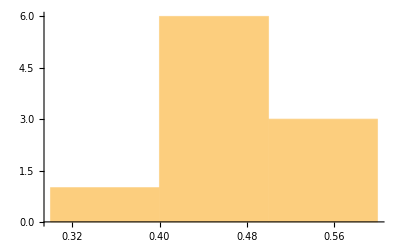

```mathematica
n=10;
data := Last[simulatePopulations[10, 10, 100, 150, 0][[1]][[2;;-1, 4]]]
dataTable=Table[data,{n}];
Histogram[dataTable]
```

```mathematica
Xbar=Mean[dataTable];
sX = StandardDeviation[dataTable];
Print["Xbar:",Xbar]
Print["sX:",sX]
Print["95% CI : ",{Xbar - 1.96 sX/Sqrt[n] , Xbar + 1.96 sX/Sqrt[n]}]
Print["Max error : ",1.96 sX/Sqrt[n]]
```

Xbar:0.474015

sX:0.0540649

95% CI : {0.440506,0.507525}

Max error : 0.0335098